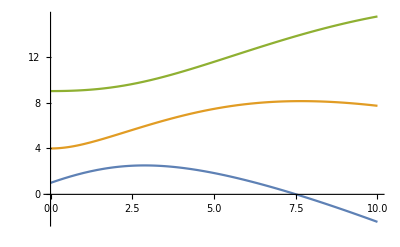

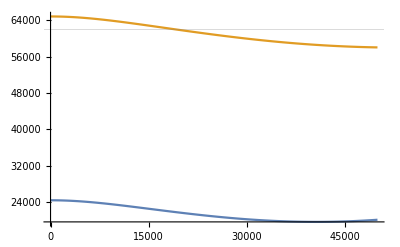

```mathematica
hPlanck=6.626*^-34;
hbar=hPlanck/2/Pi;
L1064=1064*^-9;
k1064=2*Pi/L1064;
MRb=1.44316*^-25;
Resonance=31000;
BandgapA[low_,high_,V_]:=(hbar^2*k1064^2/(2*MRb))*(MathieuCharacteristicA[high, q]-MathieuCharacteristicA[low, q])/hPlanck/.q->(V*hPlanck)*MRb/(2*hbar^2*k1064^2);
Plot[{MathieuCharacteristicA[1, q],MathieuCharacteristicA[2, q],MathieuCharacteristicA[3, q]},{q,0,10}]
Plot[{BandgapA[2,4,V],BandgapA[2,6,V]},{V,0,50000},GridLines->{None,{2*Resonance}}]
```

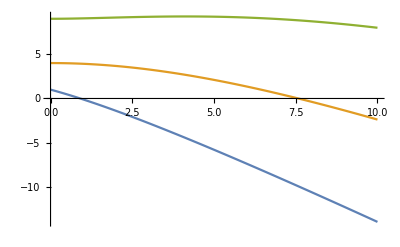

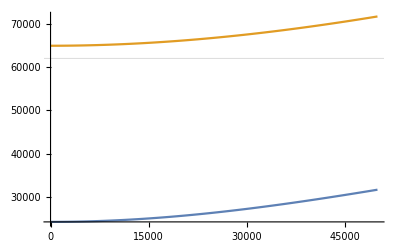

{V→46959.6}

```mathematica
BandgapB[low_,high_,V_]:=(hbar^2*k1064^2/(2*MRb))*(MathieuCharacteristicB[high, q]-MathieuCharacteristicB[low, q])/hPlanck/.q->(V*hPlanck)*MRb/(2*hbar^2*k1064^2);
Plot[{MathieuCharacteristicB[1, q],MathieuCharacteristicB[2, q],MathieuCharacteristicB[3, q]},{q,0,10}]
Plot[{BandgapB[2,4,V],BandgapB[2,6,V]},{V,0,50000},GridLines->{None,{2*Resonance}}]
FindRoot[BandgapB[2,4,V]==2*Resonance,{V,40000}]
```